# Striking A Round Drum

## A study in how PDEs aren't that scary, can have very pretty pictures, and are super useful

Partial Differential Equations Final Project
By Rebecca Jordan and Raagini Rameshwar
May 2017

#### How to use this lesson:

This lesson is designed to be interactive. It was made with Wolfram Mathematica 11.0. As a .cdf the sliders and 3D rotation of figures should be functional. This document also contains the code used to generate the figures, within hidden cells. Where the text indicates content is hidden, look at the cell markers in the right margin. A filled-in triangle indicates the hidden cell. Double-click on the bracket with the filled triangle to expand it. Try below:

(heading of a hidden cell)

Congrats! You’ve found the hidden content. Here, have a cool and relevant gif:

By expanding hidden content you can inspect the code used for calculations and to create the figures. You may need to open this document in Mathematica rather than CDF Player to make changes. Before making any changes, evaluate the entire document from the top Evaluate menu, so that variables and equations that may be referenced are stored in the workspace. Press shift+enter with your cursor in a cell to re-evaluate just that cell after making changes. You can use this for hands-on learning about both the math and Mathematica as a tool. Mathematica has excellent documentation in case you run into syntax troubles or want to extend further. I’ve also included hidden cells that suggest ways to go a little deeper with the figures mathematically. Have fun!

1. The Wave Equation

Whenever you strike a physical object, like plucking a guitar string, jumping on your bed, or even slamming a door, you cause waves through that object. Depending on specific characteristics of that object, the waves can be fast or slow, large or small, and long-lasting or ephemeral. These also depend on exactly how you strike that object. The wave equation is a mathematical model that can show us exactly how a certain object reacts to being struck in a certain way. The wave equation is, in its most simple form, u_tt = u_xx, equating the second time derivative with the second space derivative. The purpose of this paper is to show how partial differential equations help us solve the wave equation and thus gain information about what happens when we pluck strings or hit drums. There will be lots of interactive graphs and fun math, and hopefully by the end you, the reader, will have a better understanding of what the wave equation means and what it can teach us about round drums.

## a. One Dimension

In one dimension, the wave equation answers the question “what would happen if I strike or pluck a piano wire?” In general, when one plucks a wire, the wire vibrates with different frequencies that vary over time and space.The function u(t,x) describes the motion of this plucked wire, and we know that the second time derivative of u equals the second space derivative of u, or(d^2 u)/dx^2= (d^2 u)/dt^2

(expand for calculations)

f1 is the initial velocity of the wire as a function of x
af1 is the k^th term of the Fourier coefficient for approximating the initial condition, found by the convolution of the initial condition with the k^th wave building block that fulfills the boundary condition
c1 is the coefficient in the equation u_tt =cu_xx, relating to the ratio of stiffness to mass of the wire.
uc is the k^th term of the Fourier approximation (the k^th coefficient multiplied by the k^thbuilding block that fulfills the boundary conditions.)
uc1 is the sum of the first 50 terms of the Fourier approximation of the initial condition

```mathematica
f1[x_] := Piecewise[{{4 x (1 - x),  0 < x < 1}, {0, 1 ≤ x < 2}}]
af1[k_]=∫_0^2 f1[x] Sin[k/2 π x]ⅆx;
c1 = 2;
uc[x_, t_, k_] :=af1[k]/(c1 π k) Sin[ k/2  π x ]Sin[c1 k/2 π t]
uc1[x_, t_] = ∑_(k=1)^50 uc[x, t, k];
```

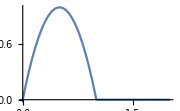

```mathematica
Plot[f1[x], {x, 0, 2}, ImageSize->Small]
```

Drag the slider to view the wave response to the initial velocity shown above. This models a piano wire with both ends pinned being struck near one end.

```mathematica
Manipulate[Plot[uc1[x, t], {x, 0, 2}, PlotRange->0.1], {t, 0, 3}]
```

#### (expand for more ways to play with this graph)

Expand the graphing code
 Plot uc instead of uc1 to look at an individual “building block” of the solution.
Expand the calculation above
 Change the upper number in the sum (currently 50) to control how many “building blocks” are summed. 
 Plot the second spatial derivative. How does it correlate to motion?
 Change c1. What effect does it have?

What this equation means lies in its derivation. The wave equation derives from the basic physical equation F = ma (Force = Mass*Acceleration). u_tt clearly corresponds to acceleration because acceleration is the second time derivative. F relates to the second space derivative by equating this plucked string to a spring with a certain tension. With springs, the force to stretch it out is dependent on how far it is stretched, (F = -kx) and observing the force on a length of wire shows us that the force is in fact (more or less) proportional to the second space derivative.

A point at the base of a concave-up curve wants to move upward, and a point at the bottom of a concave-down curve wants to move downward. Setting the two forces equal to each other tells us that the second space derivative is proportional to the second time derivative.

## b. Two Dimensions

In two dimensions, the wave equation answers the question “what would happen if I strike a membrane?” In this case, the wave equation can tell us how parameters like size, tension, and density of the membrane, and location and intensity of the initial strike affect the waves the drum makes as a function of time. The function u(t,x,y) describes the vibrations of the drum, and its PDE is u_tt=c^2 Δ^2 u. In plain English, the second time derivative of u is proportional to the Laplacian (or divgrad) of u. This wave equation is still based on the equation F=m*a. Again, u_tt corresponds to acceleration because it’s the second time derivative. Let’s explore Δ^2 u a little.

### i. Exploring Divergence, Gradient, and the Laplacian

The divergence, gradient, and Laplacian all serve as different derivatives in two dimensions. We’ll first explore the divergence and gradient separately, then think about what happens when you take the divergence of the gradient of a function, or the Laplacian of the function.

The gradient of a function is the closest to taking the derivative of a two-dimensional function. However, instead of a constant, the gradient returns a vector field that is always perpendicular to the “topographic” contours of the function. For example, if we had a function u=x^2+2 y^2, the gradient of u, or Δu=2xi + 4yj. Below is a visual representation of the gradient. Note that the gradient is a vector field, and each vector is perpendicular to the curve of u at that point. 
Gradient is written as ∇f(x) (pronounced ‘del’)

(expand for calculations)

f2 is the function currently being plotted (f2a, f2b, and f2c are provided as pretty examples)
p2b_ are graphics objects representing the plots. They are shown later.
	p2b1 is the vectors
	p2b2 is the contours/coloring
	p2b3 is the 3D plot

```mathematica
f2a[x_, y_] := x^2 - 2 y^2
f2b[x_,y_] := y Sin[x]
f2c[x_,y_] := Sin[x]Sin[2y]

f2[x_,y_]:=f2a[x,y]
p2b1 =VectorPlot[∇_{x,y} f2[x,y],{x, -1, 1}, {y, -1, 1} , VectorStyle->Black];
p2b2 = ContourPlot[f2[x,y],{x, -1, 1}, {y, -1, 1} ];
p2b3 = Plot3D[f2[x,y], {x, -1, 1}, {y, -1, 1}, MeshFunctions->{#3&}];
```

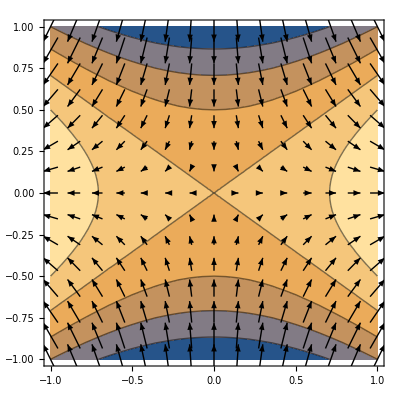

```mathematica
GraphicsGrid[{{p2b3, Show[p2b2, p2b1]}}, ImageSize->Full]
```

The colors in the graph on the right correspond to the height of the function shown on the left. The arrows are the vector-field output of the gradient operator applied to this function. They always point uphill, perpendicular to the contour lines, with the magnitude representing “steepness.” Water would flow down the function against the gradient.

#### (expand for more ways to play with the above graph)

Expand the calculation above
 Three wobbly functions are provided. All you need to change is which one f2 is set equal to, and then re-evaluate the code and the graphing code
 You will probably want to change the bounds of graphing, too.

The divergence applies to vector fields and gives us the level of "source-ness" and "sink-ness" of each point in the field. That is, the divergence shows us whether the function is flowing out of each point or into each point. Given a function u = 2xi+4yj, div(u) = 2+4=6. A positive divergence indicates outward flow, and thus a source. A negative divergence indicates inwards flow, and thus a sink. To continue the water analogy, if the original vector field is water flow, water would run off areas of positive divergence, and pool in areas of negative divergence. It would remain in a sheet (though still flowing unless the gradient is also 0) in areas of 0 divergence.
Divergence is written as ∇·f(x)  (note the dot)

(expand for calculations)

b3 is the vector field we’re starting with. 
I calculated the divergence in a separate line because Mathematica didn’t seem to want to accept it as input to the graphing function. You can see it as output.

```mathematica
b3 [x_,y_]:= {y Sin[x], -Cos[x]};
∇_{x,y} .b3[x,y]
p3b1 =VectorPlot[b3[x,y],{x, -1,1}, {y, -1, 1}, VectorStyle->Black ];
p3b2 = DensityPlot[y Cos[x],{x, -1,1}, {y, -1, 1}];
```

y Cos[x]

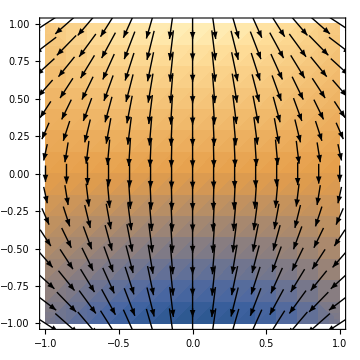

```mathematica
Show[p3b2, p3b1]
```

Note that this time, the vector field is the input and the colors are the output. Sorry, no fun interactivity for this one, unless you want to make up your own vector field input.

The Laplacian, or divgrad (∇^2), is the divergence of the gradient. It gives us the mean curvature of a function by looking at how changes in the function cause source-ess and sink-ness. Now think back to someone striking a drum. The divgrad of the motion tells us how the membrane of the drum is curving at any specific time. That curving directly relates to the restoring force of the drum head. The tighter the curve, the more force it has when it snaps back, like how rubber bands snap back tighter the more you pull them. So in the end, our new two-dimensional version of the wave equation still ties back to our old friend from physics, F=m·a.

(expand for calculations)

f4 is the function currently being plotted (f4a, f4b, and f4c are provided as pretty examples)
gf4 is the gradient of the function f3
df4 is the Laplacian of function f3 calculated directly from 
 	(output of gf4 and df4 displayed below the equations when the code is evaluated)
p4b_ are graphics objects representing the plots. They are shown later.
	p4b1 is the 3D plot
	p4b2 is the contours/coloring
	p4b3 is the 3D plot

```mathematica
f4a[x_, y_] := Sin[x]Sin[2y]
f4b[x_,y_] := y Sin[x]
f4c[x_,y_] := Sin[x^2]Sin[y]
f4d[x_,y_] := x^3-y^2

f4[x_,y_]:=f4a[x,y]
gf4[x_,y_]=∇_{x,y} f4[x,y]
df4[x_,y_]=∇_{x,y}^2 f4[x,y]

p4b1 = Plot3D[f4[x,y], {x, -π, π}, {y, -π, π}, MeshFunctions->{#3&}];
p4b2 = ContourPlot[df4[x,y],{x, -π, π}, {y, -π, π}];
p4b3 =VectorPlot[gf4[x,y],{x, -π, π}, {y, -π, π} , VectorStyle->Black];
```

{Cos[x] Sin[2 y],2 Cos[2 y] Sin[x]}

-5 Sin[x] Sin[2 y]

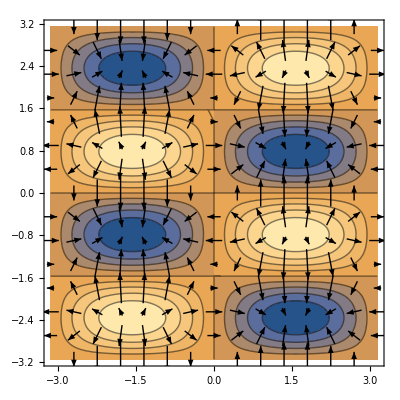

```mathematica
GraphicsGrid[{{p4b1, Show[p4b2, p4b3]}}, ImageSize->Full]
```

In the plot on the right, the vector field is the intermediate step, the gradient of the function shown in the 3D plot at left. The contour plot of colors underneath is the Laplacian of the function.

#### (expand for more ways to play with the above graph)

Expand the calculation above
 Change the code to calculate the divergence of the gradient rather than the divgrad of the original function and verify that they are the same (this can be done symbolically)
 Compare a contour plot of the function and the divgrad of the function. When are they the same and different?

II. Solving the General Wave Equation

Solving the wave equation in two dimensions means finding a function u(t,x) that fits the given equation u_tt=c^2∇^2 u. So we’re trying to find a function u whose second time derivative equals its Laplacian. From much research done by people with lots of time and mathematical passion, we know the following: u(t,x,y)=cos(ωt) ϕ(x, y) and u(t,x,y)=sin(ωt) ϕ(x, y) are both solutions, as long as ϕ(x) is an eigenfunction of the Laplacian.

Firstly, what? Let’s explore what it means to be an eigenfunction of the Laplacian and why that’s important to solving this equation. Remember that if we find a solution to the differential equation, it is the solution. That means if u(t,x) meets the criteria u_tt=c^2∇^2 u, it is the solution.

An eigenfunction of an operator L is a function α such that Lα = cα. That is, applying the operator L on α gives us that same function α times a scalar c. When you take the second time derivative of u(t,x,y) = cos(ωt)ϕ(x), you get u^(..)(t,x,y) =-ω^2cos(ωt)ϕ(x), or -ω^2u(t,x,y). It is the same result when you take the Laplacian of u, or (∂_x)^2+(∂_y)^2.Therefore, u fits the above criteria as long as ∇^2 ϕ = -ω^^2 ϕ.

Now, what functions fulfill that criteria? Again, thanks to mathematicians, we know that ϕ(x, y) can be of the form
	sin(a x) sin(b y),	 sin(a x) cos(b y), 	cos(a x) sin(b y), 	or 	cos(a x) cos(b y).
This is because those trig functions are eigenfunctions of the second derivative, and taking the Laplacian is basically like taking the second derivative in two dimensions. One way to imagine the rectangular drum is a bunch of piano wires woven so that the wave equation applies in both the x and y directions. 

What are a and b? We can figure out that ∇^2 (sin(a x) sin(b y)) = -(a^2 + b^2)(sin(a x) sin(b y)),
and we know that ∇^2 ϕ = -ω^2ϕ, so therefore ω^2 =a^2 + b^2, or ω = √(a^2 + b^2).
ω is the frequency at which our overall equation oscillates. a and b, as it turns out, are the number of nodes in the sine/cosine function in each direction. If you have a particular boundary condition to fulfill, such as a drum being pinned at the edges, a and b must be chosen carefully, just as in the 1D case.

(expand for calculations)

f5 is an eigenfunction of ∇^2

```mathematica
f5[x_, y_, t_, a_, b_] := Cos[√(a^2 + b^2) t]Sin[a x] Sin[b y];
```

```mathematica
Manipulate[Plot3D[f5[x, y, t, a,b], {x, 0, 1}, {y, 0, 1}, PlotRange->1, ImageSize->Full], {t, 0, 6}, {{a, π}, 1,3π}, {{b,π}, 1, 3π}]
```

You can drag the time slider to travel through time as you see fit, or you can press the + next to it and press play to animate it.

#### (expand for more ways to play with the above graph)

Expand the calculation above
 This code uses sines in both spatial directions and cosine for time. Try using sine for time, or cosine for one or both of the spatial dimensions.
 How do a and b affect the frequency? Does this seem physical?
 Figure out which values of a and b fulfill the boundary conditions of a 1x1 square drum (hint: you can press + and type π with [Esc] pi [Esc] into the box to get an exact value. You don’t need to type * for multiplication, 2π is understood.)
 Change either a and b or the maximum time on the slider to make the animation loop perfectly.
 Change the boundary of the drum--larger, smaller, or rectangular. Find a and b to fulfill the new boundary condition.
 Find a general rule for which a and b will fulfill a given boundary condition. How is this affected by changing around sines and cosines?

However, unless your drum’s initial condition is a perfect sinusoid like the ones above, we need to approximate it with a Fourier series as in the 1D example above. In the case of two dimensions bounded by a rectangular area, like a rectangular drum, u is the sum of many modes ϕ that vibrate with specific frequencies ω.

So solving the wave equation can be done in 3 easy steps. First, find the function ϕ that is an eigenfunction of the Laplacian and fits the given boundaries (though this should probably be done for you because mathematicians have spent a long time finding eigenfunctions). Next, write the initial condition as a linear combination of the eigenfunctions. Then multiply the linear combination by cos(ωt) or sin(ωt) depending on the initial condition. An initial condition in which the membrane is already deformed (like a plucked string) uses cosine for the time component, and an initial condition in which the membrane is flat but has some velocity (like a drum after momentum is transferred from the drumstick) uses sine.

III. Solving the Wave Equation with Radial Boundaries

#### (expand for a note on speed optimization in Mathematica)

The functions needed for a round drum go beyond sines and cosines, and finding the zeros of the Bessel function is a pretty slow operation. I found that the calculations in the following section could easily tie up my computer for 10 or more minutes, to say nothing of being able to actually recalculate quickly enough to produce an interactive animation.
So in this step I precalculate 100 zeroes of the Bessel function-- from n=0 to 9 and from m=1 to 10. In the rest of this section I will use the function defined here, β[n,m] rather than the Mathematica function BesselJZero[n,m]. The pluses and minuses scattered throughout deal with the issue of indexing from 0, since Mathematica arrays index from 1.
I’m sure there’s much more optimization possible in these functions, but this one change gives a very significant improvement.

```mathematica
βtable = Table[N[BesselJZero[i,j]], {i,Range[10]-1}, {j,Range[10]}]
β[n_, m_] :=βtable[[(n+1),m]]
```

{{2.40483,5.52008,8.65373,11.7915,14.9309,18.0711,21.2116,24.3525,27.4935,30.6346},{3.83171,7.01559,10.1735,13.3237,16.4706,19.6159,22.7601,25.9037,29.0468,32.1897},{5.13562,8.41724,11.6198,14.796,17.9598,21.117,24.2701,27.4206,30.5692,33.7165},{6.38016,9.76102,13.0152,16.2235,19.4094,22.5827,25.7482,28.9084,32.0649,35.2187},{7.58834,11.0647,14.3725,17.616,20.8269,24.019,27.1991,30.371,33.5371,36.699},{8.77148,12.3386,15.7002,18.9801,22.2178,25.4303,28.6266,31.8117,34.9888,38.1599},{9.93611,13.5893,17.0038,20.3208,23.5861,26.8202,30.0337,33.233,36.422,39.6032},{11.0864,14.8213,18.2876,21.6415,24.9349,28.1912,31.4228,34.6371,37.8387,41.0308},{12.2251,16.0378,19.5545,22.9452,26.2668,29.5457,32.7958,36.0256,39.2404,42.4439},{13.3543,17.2412,20.807,24.2339,27.5837,30.8854,34.1544,37.4001,40.6286,43.8438}}

In the case of a radial boundary, the nodes that vibrate are in the radial and angular direction. Below are examples of nodes that can occur on a circular drum head of radius 1 when it is struck. Normally, finding an eigenfunction is simply a matter of adding sines and cosines in the x and y directions. In the case of a radial boundary, it has radial and angular components. The easiest thing to do is find the eigenfunction piece by piece.

```mathematica
TableForm[Table[Plot3D[BesselJ[n-1,β[n-1,m]Norm[{x,y}]]Cos[(n-1) ArcTan[x,y]],{x,-1,1},{y,-1,1},Exclusions->None,RegionFunction->Function[{x,y},x^2+y^2≤1]],{n,4},{m,4}]]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

Note that the columns have increasing numbers of radial oscillations, while the rows have increasing numbers of peaks at a certain radius while traveling along θ. The first row is actually n=0, while the first column is m=1. The 3D plots are all rotatable.

We start with a PDE in which we’re trying to find u(t, r, Θ). We know from above that u is going to be a weighted sum of modes made up of a time-based part multiplied by a linear combination of eigenfunctions, so u=∑_nm b_nm T(ωt)ϕ(r,θ) and where T(t) is cos(ωt) or sin(ωt) as appropriate. Now ϕ is a combination of a radial and angular component, so ϕ = R(r)Θ(θ). We can solve for each of these separately, then multiply them together to find our eigenfunction ϕ.

-Graphics-

Frequency: T(ωt) → Remember that our ϕ is an eigenfunction of the Laplacian, so Δ^2 ϕ=c^2 ϕ. -c^2is the frequency at which each more oscillates, so T(ωt) is either cos(√c t) or sin(√c t).
Mode: ϕ(r, θ) → This is a combination of R(r) and Θ(θ)

We can solve for R and Θ by finding a differential equation that relates the two of them. We first start by defining the ∇^2 operation in polar coordinates. In cartesian coordinates, Δ^2 w = (∂_x)^2+(∂_y)^2. In polar coordinates, ∆^2 w=(∂_r)^2 w+1/r∂_r w+1/r^2∂_θ w. Because in our case w is an eigenfunction of ∇^2 , we know that ∇^2 w=∇^2 RΘ=-ω^2Rθ
Equating these two expressions and playing with calculus gives us that (-Θ")/Θ=r^2(R")/R+r R'/R+ω^2 r^2
So this means that (-Θ")/Θ=λ, where λ is some constant. In plain English, Θ is a function whose second derivative divided by the original function is a constant. We’re clearly looking at a sine or cosine function here. Since our boundary condition of a circle tells us that Θ(0)=Θ(2π) and Θ’(0)=Θ’(2π), we know we’re dealing with a sine or cosine with integer frequency. 

Angular Component: Θ(θ) → a linear combination of sines and cosines with integer frequency, Acos(nθ)+Bsin(nθ). Because (-Θ")/Θ=λ, n=√λ.
To solve the radial component, we need to play with the differential equation above a little to get r^2 R"+rR'+(ω^2r^2-n^2)=0. This is a special equation called the Bessel equation, whose solution is the Bessel function.

Radial Component: R(r) → represented as the nth Bessel function J_n(ωr). We know that R(1)=0 because we’re working with a drum of radius 1, so ω must be a zero of the Bessel function. Therefore, R(r)=J_n(β_nm r) where β is the nth zero of the mth Bessel function.

Final Solution: u(t,r,θ) → the multiplication of all these components summed through all possible nm, so ∑_nm b_nm T(ωt)Θ(θ)R(r), where b_nm=(∫_r ∫_θ f(r,θ)ϕ(r,θ)drdθ)/(∫_r ∫_θ ϕ^2(r,θ)drdθ)

IV. Example Problem

As a concrete example of the process above, let’s look at what happens when we hit a circular drum.

#### Framing:

Solve the wave equation u_tt= c^2∇^2u with u=0 for x^2 + y^2 = 1, no initial displacement, and initial velocity of 1 within a centered circle of radius 1/10.

Alright, what’s that mean? 
We already know the wave equation, but thanks for giving it to us again. 
u=0 for x^2 + y^2 = 1 means we’ve got a circular drum pinned at the edge.
no initial displacement means our time function will be sin(ωt) instead of cos(ωt)

#### Fourier Approximation of Initial Condition

What’s the drum look like to start out? Well, it’s flat, but what does the velocity look like?

This is best represented with a piecewise equation. Being able to input and work with piecewise functions symbolically is one of my favorite parts of Mathematica.

```mathematica
f6[r_, θ_] :=Piecewise[{{1, 0≤r<1/10}, {0, 1/10≤θ<1}}, 0]
```

Plot it just to see what it looks like. Sadly, there’s no 3D polar plot capability, so the inputs to my function are now converted from cartesian coordinates 
r = norm(x,y) and θ = arctan(x,y)

```mathematica
Plot3D[f6[Norm[{x, y}], ArcTan[x,y]], {x, -1, 1}, {y, -1, 1}, Exclusions->None, RegionFunction->Function[{x, y}, x^2 + y^2 ≤ 1]]
```

-Graphics3D-

That looks about right. Remember, this is initial velocity and not displacement. 

Now, we’ll approximate it as a sum of the modes shown above. As with the 1D equations, this means convolving the function we’re approximating with the eigenfunction representing a mode, to find a coefficient for each (n,m) combination. Note that this doesn’t include the time portion of the equation. Also note the extra r in there-- that’s because we’re integrating over the area, and the area of a circle is r ⅆr ⅆθ to account for the change in the wedge size as distance from the center increases. 

See the note at the top of section 3 for why I’m using β instead of the built-in Mathematica function BesselJZero. 
Also, how spiffy is it that I can type this in almost as you’d write it by hand? so spiffy.

```mathematica
B[n_, m_] :=(∫_0^(2π) ∫_0^1 f6[r, θ] BesselJ[n, r β[n,m]]Cos[n θ]r ⅆrⅆθ)/(∫_0^(2π) ∫_0^1 (BesselJ[n, r β[n,m]]Cos[n θ])^2 r ⅆrⅆθ)
```

Ideally, we’d sum each mode multiplied by its Fourier coefficient B up to infinity for both n and m, like so: u(r, θ) = ∑_(m=1)^∞ ∑_(n=0)^∞ B(n, m) Cos(nθ)  J_n (β_(n,m)r)
Mathematica can actually do some converging infinite sums symbolically. But it’s slow, and I’m impatient. So let’s just peek at those coefficients and see which are really big enough to matter.
The n-1 is because the n’s actually index from 0, but tables index from 1.

```mathematica
Bc =Table[B[n-1,m], {n, 4}, {m, 10}];
TableForm[Bc]
```

0.0368362 | 0.0831223 | 0.123397 | 0.154704 | 0.174877 | 0.182654 | 0.177766 | 0.160949 | 0.133866 | 0.0989599
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

Hmm, that’s interesting. Only the modes with n=0 have nonzero coefficients. Glance again at the chart of what each of these modes look like, and you’ll see why.

```mathematica
TableForm[Table[Plot3D[BesselJ[n-1,β[n-1,m]Norm[{x,y}]]Cos[(n-1) ArcTan[x,y]],{x,-1,1},{y,-1,1},Exclusions->None,RegionFunction->Function[{x,y},x^2+y^2≤1]],{n,4},{m,4}]]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

Our initial condition is nice and symmetrical, and doesn’t have any weird offcenter lumps or parts that are periodic in the θ direction. This means we really only need to sum in the m direction. I’ll leave the sum notation there, but we’re now only looking at the n=0 terms. Again, the n+1 is because of indexing.

```mathematica
u[r_, θ_, k_] := ∑_(m=1)^k ∑_(n=0)^1 Bc[[n+1,m]]Cos[n θ]BesselJ[(n), r β[n,m]]
```

I left k in there so we can watch the shape being built up.

```mathematica
Manipulate[Plot3D[u[Norm[{x,y}], ArcTan[x,y], k], {x, -1, 1}, {y, -1, 1}, PlotRange->{-0.2, 1.2},RegionFunction->Function[{x, y}, x^2 + y^2 ≤ 1]], {k, Range[9]}]
```

Remember, k=9 means the sum of the first ten terms, not the 10th term itself. And it’s not exactly flat-topped yet, but I’m going to stop there because it’s getting slow to calculate.
And there we have it, our Fourier approximation of the initial condition. The hard part of this problem is over. Now we just need to add the time component.

#### The Time Component

So, we’ve got the angular part cos(nθ)  and the radial part J_n (β_(n,m)r)  making up each mode, summed in the proper proportion B(n,m). The last part is how they move in time.

-Graphics-

The frequency ω is actually the mth zero of the nth Bessel function, β(n,m). Since we’re starting with velocity and not displacement, as we established at the beginning, the time component is sin(ω t), or sin( t β(n,m) ). This is also where the c term comes in-- the second time derivative of this entire expression only affects the sin(ωt) term. A c coefficient to ωt will “pop out”, fulfilling u_tt= c^2∇^2u. We aren’t worried about the ω also coming out, because it’s the eigenfunction.

Let’s add that last term into our sum and animate it. We’ll set an arbitrary value of c to animate, since it wasn’t specified in the problem.

```mathematica
ut[r_, θ_,t_, k_] := ∑_(m=1)^k ∑_(n=0)^1 Bc[[n+1,m]]Cos[n θ]BesselJ[(n), r β[n,m]]Sin[c t Bc[[n+1,m]]]
c=4;
```

```mathematica
Manipulate[Plot3D[ut[Norm[{x,y}], ArcTan[x,y], t, k], {x, -1, 1}, {y, -1, 1}, PlotRange->1, ImageSize->Large, RegionFunction->Function[{x, y}, x^2 + y^2 ≤ 1]], {t, 0, 20}, {{k, 2}, Range[10]}]
```

This is really slow because the calculation is so complicated, but you can get the idea. 
And that’s how it’s done!